Kitaev Chain |

Spectral Propertiespaclet:QuantumPlaybook/tutorial/KitaevChain#283481385 | Connection to the SSH Chainpaclet:QuantumPlaybook/tutorial/KitaevChain#974129267
Majorana Representationpaclet:QuantumPlaybook/tutorial/KitaevChain#399500441 |

The Kitaev chain is a prototype example of the topological superconductor. Here, we demonstrate how to examine its properties using Q3. See Kitaev (2001), Kitaev's original, for technical details of the model.

FockNumberpaclet:Q3/ref/FockNumberQ3 Package Symbol or Qpaclet:Q3/ref/QQ3 Package Symbol | Number operator
FockHoppingpaclet:Q3/ref/FockHoppingQ3 Package Symbol or Hoppaclet:Q3/ref/HopQ3 Package Symbol | Constructs the hopping Hamiltonian terms
FockPairingpaclet:Q3/ref/FockPairingQ3 Package Symbol or Pairpaclet:Q3/ref/PairQ3 Package Symbol | Constructs the pairing Hamiltonian terms
ToMajoranapaclet:Q3/ref/ToMajoranaQ3 Package Symbol | Converts Dirac fermions to Majorana fermions.
ToDiracpaclet:Q3/ref/ToDiracQ3 Package Symbol | Converts Majorana fermions to Dirac fermions. 
GraphFormpaclet:Q3/ref/GraphFormQ3 Package Symbol | Visualizes a non-interacting Hamiltonian or corresponding matrix in a graph.
ChiralGraphFormpaclet:Q3/ref/ChiralGraphFormQ3 Package Symbol | Visualizes the off-diagonal block of a matrix with chiral symmetry.

Some useful functions to study the Kitaev chain.

Load Q3.

```mathematica
<<Q3`
```

Consider some local fermion modes.

```mathematica
Let[Fermion,c]
```

```mathematica
$L=5;
```

```mathematica
cc=c[Range[1,$L]]
cccc=Join[cc,Dagger@cc]
```

{c_(,,1),c_(,,2),c_(,,3),c_(,,4),c_(,,5)}

{c_(,,1),c_(,,2),c_(,,3),c_(,,4),c_(,,5),c_(,,1)^(,,†),c_(,,2)^(,,†),c_(,,3)^(,,†),c_(,,4)^(,,†),c_(,,5)^(,,†)}

Let t, μ, and Δ denote the hopping amplitude, chemical potential, and pairing potential, respectively.

```mathematica
Let[Real,t,μ,Δ]
```

Construct the model Hamiltonian.

```mathematica
H0=-μ*Q[cc]
Hhop=-t*PlusDagger @ FockHopping[cc]
Hpair=Δ*PlusDagger @ FockPairing[cc]
HH=H0+Hhop+Hpair
```

-μ (c_(,,1)^(,,†)c_(,,1)+c_(,,2)^(,,†)c_(,,2)+c_(,,3)^(,,†)c_(,,3)+c_(,,4)^(,,†)c_(,,4)+c_(,,5)^(,,†)c_(,,5))

-t (c_(,,1)^(,,†)c_(,,2)+c_(,,2)^(,,†)c_(,,1)+c_(,,2)^(,,†)c_(,,3)+c_(,,3)^(,,†)c_(,,2)+c_(,,3)^(,,†)c_(,,4)+c_(,,4)^(,,†)c_(,,3)+c_(,,4)^(,,†)c_(,,5)+c_(,,5)^(,,†)c_(,,4))

Δ (-c_(,,2)c_(,,1)-c_(,,3)c_(,,2)-c_(,,4)c_(,,3)-c_(,,5)c_(,,4)-c_(,,1)^(,,†)c_(,,2)^(,,†)-c_(,,2)^(,,†)c_(,,3)^(,,†)-c_(,,3)^(,,†)c_(,,4)^(,,†)-c_(,,4)^(,,†)c_(,,5)^(,,†))

-Graphics-

Take a look at the connectivity of the model. Here, the black thin lines indicate single-particle tunneling and the red thick lines represent the p-wave pairing.

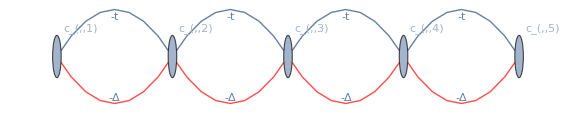

```mathematica
GraphForm[HH]
```

## Spectral Properties

To investigate the quasi-particle spectrum by means of the Bogoliubov-de Gennes (BdG) equation, obtain the single-particle BdG Hamiltonian.

```mathematica
matK=CoefficientTensor[HH,Dagger@cccc,cccc];
ArrayShort[matK,"Size"->8]
```

(-μ/2 | -t/2 | 0 | 0 | 0 | 0 | -Δ/2 | 0 | …
-t/2 | -μ/2 | -t/2 | 0 | 0 | Δ/2 | 0 | -Δ/2 | …
0 | -t/2 | -μ/2 | -t/2 | 0 | 0 | Δ/2 | 0 | …
0 | 0 | -t/2 | -μ/2 | -t/2 | 0 | 0 | Δ/2 | …
0 | 0 | 0 | -t/2 | -μ/2 | 0 | 0 | 0 | …
0 | Δ/2 | 0 | 0 | 0 | μ/2 | t/2 | 0 | …
-Δ/2 | 0 | Δ/2 | 0 | 0 | t/2 | μ/2 | t/2 | …
0 | -Δ/2 | 0 | Δ/2 | 0 | 0 | t/2 | μ/2 | …
… | … | … | … | … | … | … | … | …)

Now, study the quasi-particle energy spectrum of the model. Be aware of the finite size effects.

```mathematica
KK[a_,b_,c_]:=Block[{μ=a,t=b,Δ=c},SparseArray@ArrayRules@matK]
```

```mathematica
Manipulate[
Module[
{eval=Table[Sort@Eigenvalues[KK[μ,1.,del]],{μ,0,4,0.02}]},
ListLinePlot[Transpose@eval,
Axes->None,
Frame->True,
FrameLabel->{"μ / t","Eenergy / t"},
DataRange->{0,4}]
],
{{del,1,"Δ"},0.5,2,0.1},
SaveDefinitions->True]
```

## Majorana Representation

In this section, the Kitaev chain is expressed in terms of Majorana modes. The Majorana representation clearly reveals the chiral symmetry in the Kitaev chain.

Consider Majorana modes twice as many as the Dirac fermion modes in the above.

```mathematica
Let[Majorana,a]
```

```mathematica
aa=a@Range[2*$L]
```

{a_(,,1),a_(,,2),a_(,,3),a_(,,4),a_(,,5),a_(,,6),a_(,,7),a_(,,8),a_(,,9),a_(,,10)}

Rewrite the Hamiltonian in terms of the Majorana fermions.

```mathematica
MM=ToMajorana[HH,cc->aa]
```

-(5 μ)/2-1/2 ⅈ μ a_(,,1)a_(,,2)-1/2 ⅈ (t-Δ) a_(,,1)a_(,,4)+1/2 ⅈ (t+Δ) a_(,,2)a_(,,3)-1/2 ⅈ μ a_(,,3)a_(,,4)-1/2 ⅈ (t-Δ) a_(,,3)a_(,,6)+1/2 ⅈ (t+Δ) a_(,,4)a_(,,5)-1/2 ⅈ μ a_(,,5)a_(,,6)-1/2 ⅈ (t-Δ) a_(,,5)a_(,,8)+1/2 ⅈ (t+Δ) a_(,,6)a_(,,7)-1/2 ⅈ μ a_(,,7)a_(,,8)-1/2 ⅈ (t-Δ) a_(,,7)a_(,,10)+1/2 ⅈ (t+Δ) a_(,,8)a_(,,9)-1/2 ⅈ μ a_(,,9)a_(,,10)

Examine the connectivity through the single-particle Hamiltonian.

```mathematica
matM=CoefficientTensor[MM,aa,aa];
ArrayShort[matM,"Size"->8]
```

(0 | -(ⅈ μ)/4 | 0 | -(ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0 | 0 | …
(ⅈ μ)/4 | 0 | (ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0 | 0 | 0 | …
0 | -(ⅈ t)/4-(ⅈ Δ)/4 | 0 | -(ⅈ μ)/4 | 0 | -(ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | …
(ⅈ t)/4-(ⅈ Δ)/4 | 0 | (ⅈ μ)/4 | 0 | (ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0 | …
0 | 0 | 0 | -(ⅈ t)/4-(ⅈ Δ)/4 | 0 | -(ⅈ μ)/4 | 0 | -(ⅈ t)/4+(ⅈ Δ)/4 | …
0 | 0 | (ⅈ t)/4-(ⅈ Δ)/4 | 0 | (ⅈ μ)/4 | 0 | (ⅈ t)/4+(ⅈ Δ)/4 | 0 | …
0 | 0 | 0 | 0 | 0 | -(ⅈ t)/4-(ⅈ Δ)/4 | 0 | -(ⅈ μ)/4 | …
0 | 0 | 0 | 0 | (ⅈ t)/4-(ⅈ Δ)/4 | 0 | (ⅈ μ)/4 | 0 | …
… | … | … | … | … | … | … | … | …)

Here, factor 4ⅈ is just for convenience as it simplifies the coefficients.

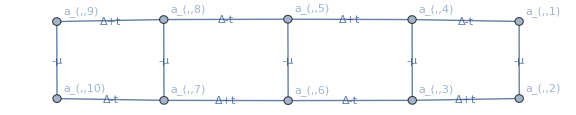

```mathematica
GraphForm[4*I*matM//SimplifyThrough,VertexLabels->aa]
```

The chiral symmetry (i.e., anti-symmetry or sub-lattice symmetry) becomes clearer by first consider the special case t=Δ as below.

### Special Case: t=Δ

Let us consider a special case: t=Δ.

```mathematica
JJ=Block[{Δ=t},MM]
```

-(5 μ)/2-1/2 ⅈ μ a_(,,1)a_(,,2)+ⅈ t a_(,,2)a_(,,3)-1/2 ⅈ μ a_(,,3)a_(,,4)+ⅈ t a_(,,4)a_(,,5)-1/2 ⅈ μ a_(,,5)a_(,,6)+ⅈ t a_(,,6)a_(,,7)-1/2 ⅈ μ a_(,,7)a_(,,8)+ⅈ t a_(,,8)a_(,,9)-1/2 ⅈ μ a_(,,9)a_(,,10)

Examine the connectivity.

```mathematica
matJ=CoefficientTensor[JJ,aa,aa];
ArrayShort[matJ,"Size"->8]
```

(0 | -(ⅈ μ)/4 | 0 | 0 | 0 | 0 | 0 | 0 | …
(ⅈ μ)/4 | 0 | (ⅈ t)/2 | 0 | 0 | 0 | 0 | 0 | …
0 | -(ⅈ t)/2 | 0 | -(ⅈ μ)/4 | 0 | 0 | 0 | 0 | …
0 | 0 | (ⅈ μ)/4 | 0 | (ⅈ t)/2 | 0 | 0 | 0 | …
0 | 0 | 0 | -(ⅈ t)/2 | 0 | -(ⅈ μ)/4 | 0 | 0 | …
0 | 0 | 0 | 0 | (ⅈ μ)/4 | 0 | (ⅈ t)/2 | 0 | …
0 | 0 | 0 | 0 | 0 | -(ⅈ t)/2 | 0 | -(ⅈ μ)/4 | …
0 | 0 | 0 | 0 | 0 | 0 | (ⅈ μ)/4 | 0 | …
… | … | … | … | … | … | … | … | …)

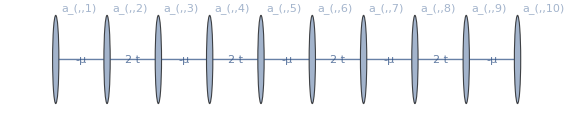

```mathematica
GraphForm[4*I*matJ//SimplifyThrough,VertexLabels->aa]
```

The above graph clearly shows the chiral (i.e. sublattice) symmetry. To make it clearer, rearrange the Majorana modes.

```mathematica
ab=Transpose@Partition[aa,2]
```

{{a_(,,1),a_(,,3),a_(,,5),a_(,,7),a_(,,9)},{a_(,,2),a_(,,4),a_(,,6),a_(,,8),a_(,,10)}}

```mathematica
matC=CoefficientTensor[JJ,Flatten@ab,Flatten@ab];
ArrayShort[matC,"Size"->8]
```

(0 | 0 | 0 | 0 | 0 | -(ⅈ μ)/4 | 0 | 0 | …
0 | 0 | 0 | 0 | 0 | -(ⅈ t)/2 | -(ⅈ μ)/4 | 0 | …
0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/2 | -(ⅈ μ)/4 | …
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/2 | …
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | …
(ⅈ μ)/4 | (ⅈ t)/2 | 0 | 0 | 0 | 0 | 0 | 0 | …
0 | (ⅈ μ)/4 | (ⅈ t)/2 | 0 | 0 | 0 | 0 | 0 | …
0 | 0 | (ⅈ μ)/4 | (ⅈ t)/2 | 0 | 0 | 0 | 0 | …
… | … | … | … | … | … | … | … | …)

The  block-off diagonal structure of the above matrix demonstrates the chiral symmetry.

```mathematica
matD=CoefficientTensor[JJ,First@ab,Last@ab];
ArrayShort[matD,"Size"->8]
```

(-(ⅈ μ)/2 | 0 | 0 | 0 | 0
-ⅈ t | -(ⅈ μ)/2 | 0 | 0 | 0
0 | -ⅈ t | -(ⅈ μ)/2 | 0 | 0
0 | 0 | -ⅈ t | -(ⅈ μ)/2 | 0
0 | 0 | 0 | -ⅈ t | -(ⅈ μ)/2)

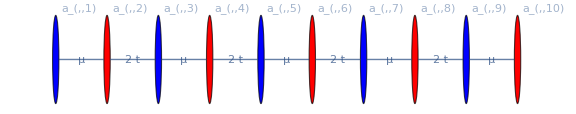

```mathematica
ChiralGraphForm[2*I*matD,VertexLabels->ab]
```

### Back to General Case

Motivated by the above special case, we now examine again the general case with the rearranged Majorana modes. The chiral symmetry is clear now.

```mathematica
matMa=CoefficientTensor[MM,Flatten@ab,Flatten@ab];
matMa//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | -(ⅈ μ)/4 | -(ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(ⅈ t)/4-(ⅈ Δ)/4 | -(ⅈ μ)/4 | -(ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/4-(ⅈ Δ)/4 | -(ⅈ μ)/4 | -(ⅈ t)/4+(ⅈ Δ)/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/4-(ⅈ Δ)/4 | -(ⅈ μ)/4 | -(ⅈ t)/4+(ⅈ Δ)/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/4-(ⅈ Δ)/4 | -(ⅈ μ)/4
(ⅈ μ)/4 | (ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(ⅈ t)/4-(ⅈ Δ)/4 | (ⅈ μ)/4 | (ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (ⅈ t)/4-(ⅈ Δ)/4 | (ⅈ μ)/4 | (ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (ⅈ t)/4-(ⅈ Δ)/4 | (ⅈ μ)/4 | (ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (ⅈ t)/4-(ⅈ Δ)/4 | (ⅈ μ)/4 | 0 | 0 | 0 | 0 | 0)

```mathematica
matN=CoefficientTensor[MM,First@ab,Last@ab];
matN//ArrayShort
```

(-(ⅈ μ)/2 | -1/2 ⅈ (t-Δ) | 0 | 0 | …
-1/2 ⅈ (t+Δ) | -(ⅈ μ)/2 | -1/2 ⅈ (t-Δ) | 0 | …
0 | -1/2 ⅈ (t+Δ) | -(ⅈ μ)/2 | -1/2 ⅈ (t-Δ) | …
0 | 0 | -1/2 ⅈ (t+Δ) | -(ⅈ μ)/2 | …
… | … | … | … | …)

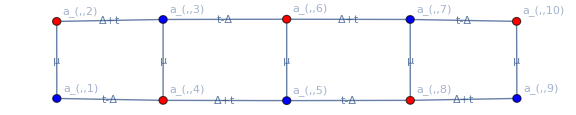

```mathematica
ChiralGraphForm[2*I*matN,VertexLabels->ab]
```

## Connection to the SSH Chain

Two copies of the Kitaev chain is equivalent to the the Su-Schrieffer-Heeger (SSH) chain; i.e., (Kitaev)⊗(Kitaev)≃(SSH). See, for example, Shapourian and Ryu (2017)https://doi.org/10.1103/PhysRevB.95.165101 and Chiu et al. (2016)https://doi.org/10.1103/RevModPhys.88.035005.

Consider two sets of Majorana modes.

```mathematica
Let[Majorana,a,b]
```

```mathematica
aa=a[Range[2$L]]
bb=b[Range[2$L]]
```

{a_(,,1),a_(,,2),a_(,,3),a_(,,4),a_(,,5),a_(,,6),a_(,,7),a_(,,8),a_(,,9),a_(,,10)}

{b_(,,1),b_(,,2),b_(,,3),b_(,,4),b_(,,5),b_(,,6),b_(,,7),b_(,,8),b_(,,9),b_(,,10)}

Construct a two copies of the Kitaev chain.

```mathematica
DD=MultiplyDot[aa,matM.aa]+MultiplyDot[bb,matM.bb]
```

-1/2 ⅈ μ a_(,,1)a_(,,2)-1/2 ⅈ (t-Δ) a_(,,1)a_(,,4)+1/2 ⅈ (t+Δ) a_(,,2)a_(,,3)-1/2 ⅈ μ a_(,,3)a_(,,4)-1/2 ⅈ (t-Δ) a_(,,3)a_(,,6)+1/2 ⅈ (t+Δ) a_(,,4)a_(,,5)-1/2 ⅈ μ a_(,,5)a_(,,6)-1/2 ⅈ (t-Δ) a_(,,5)a_(,,8)+1/2 ⅈ (t+Δ) a_(,,6)a_(,,7)-1/2 ⅈ μ a_(,,7)a_(,,8)-1/2 ⅈ (t-Δ) a_(,,7)a_(,,10)+1/2 ⅈ (t+Δ) a_(,,8)a_(,,9)-1/2 ⅈ μ a_(,,9)a_(,,10)-1/2 ⅈ μ b_(,,1)b_(,,2)-1/2 ⅈ (t-Δ) b_(,,1)b_(,,4)+1/2 ⅈ (t+Δ) b_(,,2)b_(,,3)-1/2 ⅈ μ b_(,,3)b_(,,4)-1/2 ⅈ (t-Δ) b_(,,3)b_(,,6)+1/2 ⅈ (t+Δ) b_(,,4)b_(,,5)-1/2 ⅈ μ b_(,,5)b_(,,6)-1/2 ⅈ (t-Δ) b_(,,5)b_(,,8)+1/2 ⅈ (t+Δ) b_(,,6)b_(,,7)-1/2 ⅈ μ b_(,,7)b_(,,8)-1/2 ⅈ (t-Δ) b_(,,7)b_(,,10)+1/2 ⅈ (t+Δ) b_(,,8)b_(,,9)-1/2 ⅈ μ b_(,,9)b_(,,10)

Now, fuse pairs of Majorana  fermions across the two copies of the Kitaev chain to form Dirac fermions.

```mathematica
Let[Fermion,d]
```

```mathematica
dd=d[Range[2$L]]
```

{d_(,,1),d_(,,2),d_(,,3),d_(,,4),d_(,,5),d_(,,6),d_(,,7),d_(,,8),d_(,,9),d_(,,10)}

```mathematica
rr=ToDirac[Riffle[aa,bb]->dd]
```

{a_(,,1)→d_(,,1)+d_(,,1)^(,,†),b_(,,1)→-ⅈ (d_(,,1)-d_(,,1)^(,,†)),a_(,,2)→d_(,,2)+d_(,,2)^(,,†),b_(,,2)→-ⅈ (d_(,,2)-d_(,,2)^(,,†)),a_(,,3)→d_(,,3)+d_(,,3)^(,,†),b_(,,3)→-ⅈ (d_(,,3)-d_(,,3)^(,,†)),a_(,,4)→d_(,,4)+d_(,,4)^(,,†),b_(,,4)→-ⅈ (d_(,,4)-d_(,,4)^(,,†)),a_(,,5)→d_(,,5)+d_(,,5)^(,,†),b_(,,5)→-ⅈ (d_(,,5)-d_(,,5)^(,,†)),a_(,,6)→d_(,,6)+d_(,,6)^(,,†),b_(,,6)→-ⅈ (d_(,,6)-d_(,,6)^(,,†)),a_(,,7)→d_(,,7)+d_(,,7)^(,,†),b_(,,7)→-ⅈ (d_(,,7)-d_(,,7)^(,,†)),a_(,,8)→d_(,,8)+d_(,,8)^(,,†),b_(,,8)→-ⅈ (d_(,,8)-d_(,,8)^(,,†)),a_(,,9)→d_(,,9)+d_(,,9)^(,,†),b_(,,9)→-ⅈ (d_(,,9)-d_(,,9)^(,,†)),a_(,,10)→d_(,,10)+d_(,,10)^(,,†),b_(,,10)→-ⅈ (d_(,,10)-d_(,,10)^(,,†))}

Fuse the pairs of Majorana fermions across the two Kitaev chains. That is, rewrite the Hamiltonian for the double Kitaev chain in terms of Dirac fermions.

```mathematica
new=mm/.rr//Garner
```

-ⅈ μ d_(,,1)^(,,†)d_(,,2)-ⅈ (t-Δ) d_(,,1)^(,,†)d_(,,4)+ⅈ μ d_(,,2)^(,,†)d_(,,1)+ⅈ (t+Δ) d_(,,2)^(,,†)d_(,,3)-ⅈ (t+Δ) d_(,,3)^(,,†)d_(,,2)-ⅈ μ d_(,,3)^(,,†)d_(,,4)-ⅈ (t-Δ) d_(,,3)^(,,†)d_(,,6)+ⅈ (t-Δ) d_(,,4)^(,,†)d_(,,1)+ⅈ μ d_(,,4)^(,,†)d_(,,3)+ⅈ (t+Δ) d_(,,4)^(,,†)d_(,,5)-ⅈ (t+Δ) d_(,,5)^(,,†)d_(,,4)-ⅈ μ d_(,,5)^(,,†)d_(,,6)-ⅈ (t-Δ) d_(,,5)^(,,†)d_(,,8)+ⅈ (t-Δ) d_(,,6)^(,,†)d_(,,3)+ⅈ μ d_(,,6)^(,,†)d_(,,5)+ⅈ (t+Δ) d_(,,6)^(,,†)d_(,,7)-ⅈ (t+Δ) d_(,,7)^(,,†)d_(,,6)-ⅈ μ d_(,,7)^(,,†)d_(,,8)-ⅈ (t-Δ) d_(,,7)^(,,†)d_(,,10)+ⅈ (t-Δ) d_(,,8)^(,,†)d_(,,5)+ⅈ μ d_(,,8)^(,,†)d_(,,7)+ⅈ (t+Δ) d_(,,8)^(,,†)d_(,,9)-ⅈ (t+Δ) d_(,,9)^(,,†)d_(,,8)-ⅈ μ d_(,,9)^(,,†)d_(,,10)+ⅈ (t-Δ) d_(,,10)^(,,†)d_(,,7)+ⅈ μ d_(,,10)^(,,†)d_(,,9)

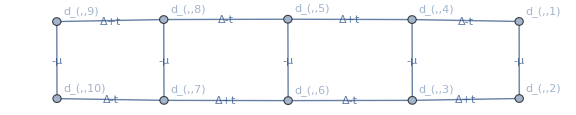

```mathematica
GraphForm[I*new]
```

```mathematica
cd=Transpose@Partition[dd,2]
```

{{d_(,,1),d_(,,3),d_(,,5),d_(,,7),d_(,,9)},{d_(,,2),d_(,,4),d_(,,6),d_(,,8),d_(,,10)}}

```mathematica
matF=CoefficientTensor[new,Dagger@First@cd,Last@cd];
matF//ArrayShort
```

(-ⅈ μ | -ⅈ (t-Δ) | 0 | 0 | …
-ⅈ (t+Δ) | -ⅈ μ | -ⅈ (t-Δ) | 0 | …
0 | -ⅈ (t+Δ) | -ⅈ μ | -ⅈ (t-Δ) | …
0 | 0 | -ⅈ (t+Δ) | -ⅈ μ | …
… | … | … | … | …)

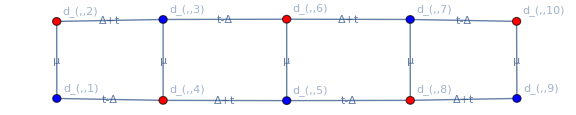

```mathematica
ChiralGraphForm[I*matF,VertexLabels->cd]
```

Now, consider the special case t=Δ.

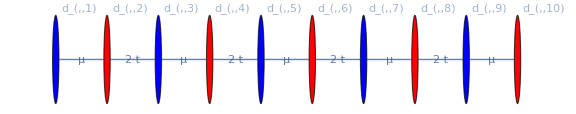

```mathematica
ChiralGraphForm[ReplaceAllThrough[I*matF,Δ->t],VertexLabels->cd]
```

| Related Guides
▪Quantum Many-Body Systems

| Related Tech Notes
▪Quantum Many-Body Systems with Q3
▪Q3: Quick Start

| Related Links
▪H. Shapourian and S. Ryu (2017)https://doi.org/10.1103/PhysRevB.95.165101, Physical Review B 95, 165101 (2017), "Partial time-reversal transformation and entanglement negativity in fermionic systems."
▪C.-K. Chiu et al. (2016)https://doi.org/10.1103/RevModPhys.88.035005, Review of Modern Physics 88, 035005 (2016), "Classification of topological quantum matter with symmetries."
▪A. Kitaev, Physics-Uspekhi 44, 131 (2001)https://doi.org/10.1070/1063-7869/44/10S/S29, "Unpaired Majorana fermions in quantum wires".
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).